## Potential solutions (Poisson)

```mathematica
(*outer*)ϕ3[r_]:=(λD BesselK[0,r/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselI[0,R1/λD]+R1 R2 ϵ σ2 BesselI[1,R1/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
(*inner*)ϕ1[r_]:=(λD BesselI[0,r/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
(*MT wall*)ϕ2[r_]:=(R1 R2 ϵ λD σ2 BesselI[1,R1/λD] BesselK[0,R2/λD] Log[r/R1]+λD BesselI[0,R1/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] (-Log[r/R1]+Log[R2/R1])))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

## parameters

```mathematica
R2=12.5*^-9
```

1.25×10^-8

```mathematica
R1=7.5*^-9
```

7.5×10^-9

```mathematica
ϵ0=N[QuantityMagnitude[UnitConvert[Quantity["ElectricConstant"],"SIBase"]]]
```

8.85419×10^-12

```mathematica
ϵ=9*ϵ0 (*cytoplasm*)
```

7.96877×10^-11

```mathematica
ϵ2=2*ϵ0 (*mt wall*)
```

1.77084×10^-11

```mathematica
R=8.314462618  (*J/(mol*K)*)
```

8.31446

```mathematica
(*R = QuantityMagnitude[UnitConvert[Quantity["GasConstant"],"SIBase"]]*)
```

```mathematica
F=QuantityMagnitude[UnitConvert[Quantity["FaradayConstant"],"SIBase"]]
```

120606665154137523/1250000000000

```mathematica
T=310
```

310

```mathematica
iccc1bulk=140;    (* K+ ------->140 mM = 140 mol/m^3 *)
iccc2bulk=12;    (* Na+ ------->12 mM = 12 mol/m^3 *)
iccc3bulk=4;    (* Cl- ------->4 mM = 4 mol/m^3 *)
iccc4bulk=74;    (* HPO4(-2) ------->74 mM = 74 mol/m^3 *)

(*Charge number of the species - Ion Valency*)
z1=1;  (* K+ *)
z2=1; (* Na+ *)
z3=-1; (* Cl- *)
z4=-2;(* HPO4(-2) *)
```

```mathematica
λD=Sqrt[ϵ *R*T/F^2/(z1^2*iccc1bulk+z2^2*iccc2bulk+z3^2*iccc3bulk+z4^2*iccc4bulk)]
```

2.20934×10^-10

```mathematica
σ1=-0.025(*C/m^2*)
```

-0.025

```mathematica
σ2=-0.083(*C/m^2*)
```

-0.083

## C10-Outer capacitance

```mathematica
ϕ3sigma[σ2_]:=(λD BesselK[0,R2/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselI[0,R1/λD]+R1 R2 ϵ σ2 BesselI[1,R1/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
sigma2data=Table[i,{i,-0.086,-0.080,0.001}]
```

{-0.086,-0.085,-0.084,-0.083,-0.082,-0.081,-0.08}

```mathematica
ϕ3data=ϕ3sigma/@sigma2data
```

{-0.235116,-0.232388,-0.22966,-0.226932,-0.224205,-0.221477,-0.218749}

```mathematica
Cdata1=Transpose[{ϕ3data,sigma2data}]
```

{{-0.235116,-0.086},{-0.232388,-0.085},{-0.22966,-0.084},{-0.226932,-0.083},{-0.224205,-0.082},{-0.221477,-0.081},{-0.218749,-0.08}}

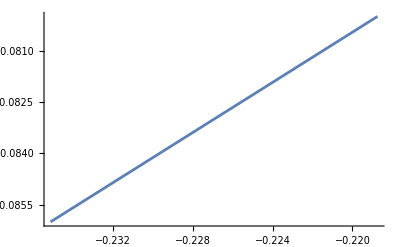

```mathematica
ListLinePlot[Cdata1]
```

```mathematica
fit1=Fit[Cdata1,{1,x},x]
```

0.000192614+0.366596 x

```mathematica
Cd1=Coefficient[fit1,x]
```

0.366596

```mathematica
l=8*^-9
```

1/125000000

```mathematica
C10=Cd1*2*π*R2*l
```

2.30339×10^-16

## C20-Inner Capacitance

```mathematica
ϕ1sigma[σ1_]:=(λD BesselI[0,R1/λD] (ϵ2 λD (R1 σ1+R2 σ2) BesselK[0,R2/λD]+R1 R2 ϵ σ1 BesselK[1,R2/λD] Log[R2/R1]))/(R2 ϵ ϵ2 λD BesselI[0,R1/λD] BesselK[1,R2/λD]+R1 ϵ BesselI[1,R1/λD] (ϵ2 λD BesselK[0,R2/λD]+R2 ϵ BesselK[1,R2/λD] Log[R2/R1]));
```

```mathematica
sigma1data=Table[i,{i,-0.030,-0.020,0.001}]
```

{-0.03,-0.029,-0.028,-0.027,-0.026,-0.025,-0.024,-0.023,-0.022,-0.021,-0.02}

```mathematica
ϕ1data=ϕ1sigma/@sigma1data
```

{-0.0862593,-0.0834809,-0.0807025,-0.0779241,-0.0751457,-0.0723673,-0.0695889,-0.0668105,-0.0640321,-0.0612537,-0.0584753}

```mathematica
Cdata2=Transpose[{ϕ1data,sigma1data}]
```

{{-0.0862593,-0.03},{-0.0834809,-0.029},{-0.0807025,-0.028},{-0.0779241,-0.027},{-0.0751457,-0.026},{-0.0723673,-0.025},{-0.0695889,-0.024},{-0.0668105,-0.023},{-0.0640321,-0.022},{-0.0612537,-0.021},{-0.0584753,-0.02}}

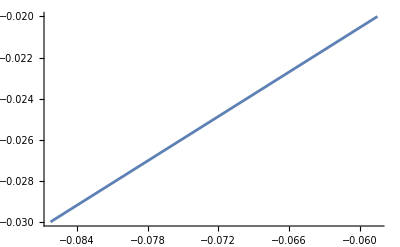

```mathematica
ListLinePlot[Cdata2]
```

```mathematica
fit2=Fit[Cdata2,{1,x},x]
```

0.00104639+0.359919 x

```mathematica
Cd2=Coefficient[fit2,x]
```

0.359919

```mathematica
C20=Cd2*2*π*R1*l
```

1.35686×10^-16